# DATA ANALYSIS

Descriptive analysis of DATA.csv (100 subjects, 9 columns). Column roles, plot labels, and category decodes follow DATA_DICTIONARY.md.

## LOAD DATA

Import the CSV from the notebook's own folder as a Datasetpaclet:ref/Datasethttps://reference.wolfram.com/language/ref/Dataset.html.

```mathematica
data=Import[FileNameJoin[{NotebookDirectory[],"DATA.csv"}],"Dataset",HeaderLines->1];
data
```

Sanity check: the dataset should have 100 rows and 9 columns.

```mathematica
dataDimensions=Dimensions[data]
```

{100,9}

```mathematica
columnNames=Normal[Keys[First[data]]]
```

{ID,Age,Chol,DBP,Temp,Group,Survey,DiabetesMellitus,EssentialHypertension}

## UNIVARIATE DATA ANALYSIS

Each column is described on its own, in CSV column order, using statistics that match its role in the data dictionary.

### ID

ID is an identifier, so it only receives a uniqueness and completeness check.

```mathematica
idCol=Normal[data[All,"ID"]];
Dataset[<|
  "Number of values"->Length[idCol],
  "Number of unique values"->CountDistinct[idCol],
  "All values unique"->DuplicateFreeQ[idCol],
  "Number of missing values"->Count[idCol,_Missing | ""],
  "All values are integers"->AllTrue[idCol,IntegerQ],
  "Values are exactly 1 to n"->(Sort[idCol]===Range[Length[idCol]])
|>]
```

### AGE

Continuous (years).

```mathematica
ageCol=Normal[data[All,"Age"]];
Dataset[<|
  "Mean"->N[Mean[ageCol]],
  "Median"->N[Median[ageCol]],
  "StandardDeviation"->N[StandardDeviation[ageCol]],
  "Quartiles"->N[Quartiles[ageCol]],
  "Min"->Min[ageCol],
  "Max"->Max[ageCol]
|>]
```

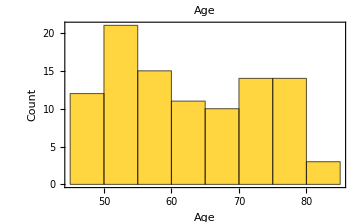

```mathematica
ageBins={45,85,5};
Histogram[ageCol,ageBins,
  Frame->True,FrameLabel->{"Age","Count"},PlotLabel->"Age",ImageSize->Medium]
```

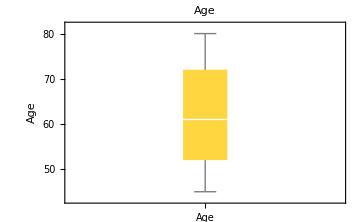

```mathematica
BoxWhiskerChart[ageCol,"Outliers",
  ChartLabels->{"Age"},Frame->True,FrameLabel->{None,"Age"},PlotLabel->"Age",ImageSize->Medium]
```

### CHOL

Continuous (mg/dL).

```mathematica
cholCol=Normal[data[All,"Chol"]];
Dataset[<|
  "Mean"->N[Mean[cholCol]],
  "Median"->N[Median[cholCol]],
  "StandardDeviation"->N[StandardDeviation[cholCol]],
  "Quartiles"->N[Quartiles[cholCol]],
  "Min"->Min[cholCol],
  "Max"->Max[cholCol]
|>]
```

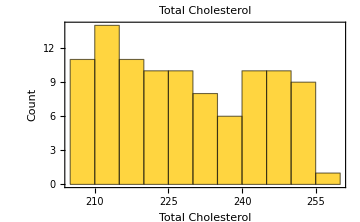

```mathematica
cholBins={205,260,5};
Histogram[cholCol,cholBins,
  Frame->True,FrameLabel->{"Total Cholesterol","Count"},PlotLabel->"Total Cholesterol",ImageSize->Medium]
```

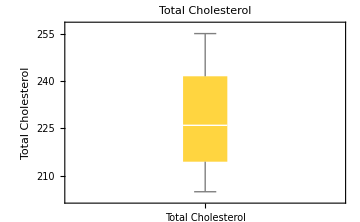

```mathematica
BoxWhiskerChart[cholCol,"Outliers",
  ChartLabels->{"Total Cholesterol"},Frame->True,FrameLabel->{None,"Total Cholesterol"},
  PlotLabel->"Total Cholesterol",ImageSize->Medium]
```

### DBP

Continuous (mmHg).

```mathematica
dbpCol=Normal[data[All,"DBP"]];
Dataset[<|
  "Mean"->N[Mean[dbpCol]],
  "Median"->N[Median[dbpCol]],
  "StandardDeviation"->N[StandardDeviation[dbpCol]],
  "Quartiles"->N[Quartiles[dbpCol]],
  "Min"->Min[dbpCol],
  "Max"->Max[dbpCol]
|>]
```

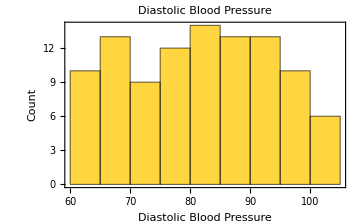

```mathematica
dbpBins={60,105,5};
Histogram[dbpCol,dbpBins,
  Frame->True,FrameLabel->{"Diastolic Blood Pressure","Count"},PlotLabel->"Diastolic Blood Pressure",
  ImageSize->Medium]
```

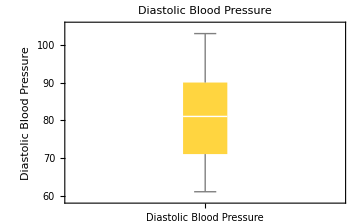

```mathematica
BoxWhiskerChart[dbpCol,"Outliers",
  ChartLabels->{"Diastolic Blood Pressure"},Frame->True,FrameLabel->{None,"Diastolic Blood Pressure"},
  PlotLabel->"Diastolic Blood Pressure",ImageSize->Medium]
```

### TEMP

Continuous (°F). Values are recorded to 0.1 °F, so the bins are centred on those recorded values.

```mathematica
tempCol=Normal[data[All,"Temp"]];
Dataset[<|
  "Mean"->Mean[tempCol],
  "Median"->Median[tempCol],
  "StandardDeviation"->StandardDeviation[tempCol],
  "Quartiles"->Quartiles[tempCol],
  "Min"->Min[tempCol],
  "Max"->Max[tempCol]
|>]
```

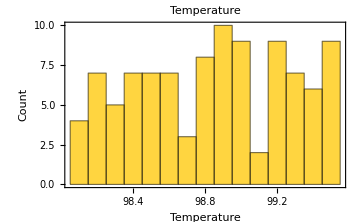

```mathematica
tempBins={98.05,99.55,0.1};
Histogram[tempCol,tempBins,
  Frame->True,FrameLabel->{"Temperature","Count"},PlotLabel->"Temperature",ImageSize->Medium]
```

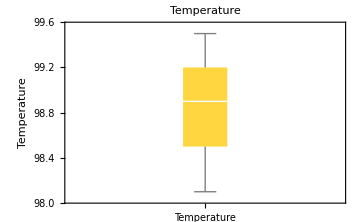

```mathematica
BoxWhiskerChart[tempCol,"Outliers",
  ChartLabels->{"Temperature"},Frame->True,FrameLabel->{None,"Temperature"},
  PlotLabel->"Temperature",ImageSize->Medium]
```

### GROUP

Categorical (nominal, 2 levels).

```mathematica
groupCol=Normal[data[All,"Group"]];
groupLevels={"Intervention","Placebo"};
groupCounts=Counts[groupCol]
```

<|Intervention→40,Placebo→60|>

```mathematica
Dataset[AssociationMap[
  <|"Count"->Lookup[groupCounts,#,0],"Proportion"->N[Lookup[groupCounts,#,0]/Length[groupCol]]|> &,
  groupLevels]]
```

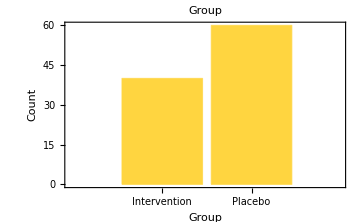

```mathematica
BarChart[Lookup[groupCounts,groupLevels,0],
  ChartLabels->groupLevels,Frame->True,FrameLabel->{"Group","Count"},PlotLabel->"Group",
  ImageSize->Medium]
```

### SURVEY

Ordinal (5 levels), so counts, proportions, mode, and median are reported rather than only a mean.

```mathematica
surveyCol=Normal[data[All,"Survey"]];
surveyLevels=Range[5];
surveyDecode=<|1->"Strongly Disagree",2->"Disagree",3->"Neither",4->"Agree",5->"Strongly Agree"|>;
surveyCounts=Counts[surveyCol];
KeySort[surveyCounts]
```

<|1→20,2→21,3→21,4→23,5→15|>

```mathematica
Dataset[AssociationMap[
  <|"Count"->Lookup[surveyCounts,#,0],"Proportion"->N[Lookup[surveyCounts,#,0]/Length[surveyCol]]|> &,
  surveyLevels] // KeyMap[surveyDecode]]
```

```mathematica
Dataset[<|
  "Mode"->(surveyDecode /@ Commonest[surveyCol]),
  "Median (score)"->Median[surveyCol],
  "Median (label)"->Lookup[surveyDecode,Median[surveyCol],"Between levels"]
|>]
```

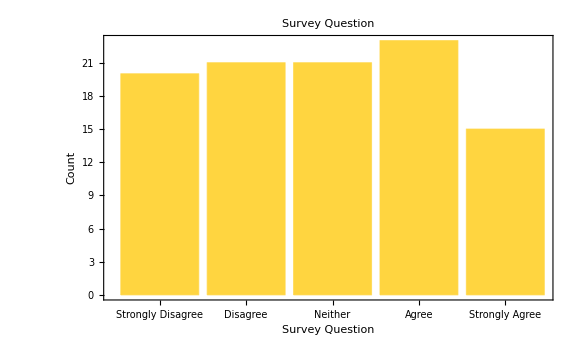

```mathematica
BarChart[Lookup[surveyCounts,surveyLevels,0],
  ChartLabels->Lookup[surveyDecode,surveyLevels],Frame->True,FrameLabel->{"Survey Question","Count"},
  PlotLabel->"Survey Question",ImageSize->Large]
```

### DIABETESMELLITUS

Categorical (nominal, 2 levels), stored as "Y"/"N".

```mathematica
dmCol=Normal[data[All,"DiabetesMellitus"]];
dmLevels={"Y","N"};
dmDecode=<|"Y"->"Yes","N"->"No"|>;
dmCounts=Counts[dmCol]
```

<|Y→51,N→49|>

```mathematica
Dataset[AssociationMap[
  <|"Count"->Lookup[dmCounts,#,0],"Proportion"->N[Lookup[dmCounts,#,0]/Length[dmCol]]|> &,
  dmLevels] // KeyMap[dmDecode]]
```

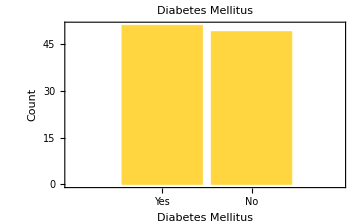

```mathematica
BarChart[Lookup[dmCounts,dmLevels,0],
  ChartLabels->Lookup[dmDecode,dmLevels],Frame->True,FrameLabel->{"Diabetes Mellitus","Count"},
  PlotLabel->"Diabetes Mellitus",ImageSize->Medium]
```

### ESSENTIALHYPERTENSION

Categorical (binary), stored as 0/1 but not treated as a number.

```mathematica
ehCol=Normal[data[All,"EssentialHypertension"]];
ehLevels={0,1};
ehDecode=<|0->"No",1->"Yes"|>;
ehCounts=Counts[ehCol]
```

<|1→45,0→55|>

```mathematica
Dataset[AssociationMap[
  <|"Count"->Lookup[ehCounts,#,0],"Proportion"->N[Lookup[ehCounts,#,0]/Length[ehCol]]|> &,
  ehLevels] // KeyMap[ehDecode]]
```

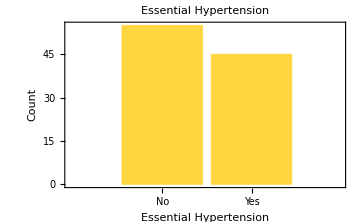

```mathematica
BarChart[Lookup[ehCounts,ehLevels,0],
  ChartLabels->Lookup[ehDecode,ehLevels],Frame->True,FrameLabel->{"Essential Hypertension","Count"},
  PlotLabel->"Essential Hypertension",ImageSize->Medium]
```

## COMPARATIVE DATA ANALYSIS

The response variable is DiabetesMellitus. Every other measured column is compared side by side between subjects with ("Y") and without ("N") diabetes mellitus. Proportions are computed within each response category.

```mathematica
dmYesData=Select[data,#DiabetesMellitus==="Y" &];
dmNoData=Select[data,#DiabetesMellitus==="N" &];
dmYesLabel="Diabetes Mellitus: " <> dmDecode["Y"];
dmNoLabel="Diabetes Mellitus: " <> dmDecode["N"];
<|dmYesLabel->Length[dmYesData],dmNoLabel->Length[dmNoData]|>
```

<|Diabetes Mellitus: Yes→51,Diabetes Mellitus: No→49|>

### AGE

```mathematica
ageColDMYes=Normal[dmYesData[All,"Age"]];
ageColDMNo=Normal[dmNoData[All,"Age"]];
Dataset[<|
  dmYesLabel-><|"Mean"->N[Mean[ageColDMYes]],"Median"->N[Median[ageColDMYes]],
    "StandardDeviation"->N[StandardDeviation[ageColDMYes]],"Quartiles"->N[Quartiles[ageColDMYes]],
    "Min"->Min[ageColDMYes],"Max"->Max[ageColDMYes]|>,
  dmNoLabel-><|"Mean"->N[Mean[ageColDMNo]],"Median"->N[Median[ageColDMNo]],
    "StandardDeviation"->N[StandardDeviation[ageColDMNo]],"Quartiles"->N[Quartiles[ageColDMNo]],
    "Min"->Min[ageColDMNo],"Max"->Max[ageColDMNo]|>
|>]
```

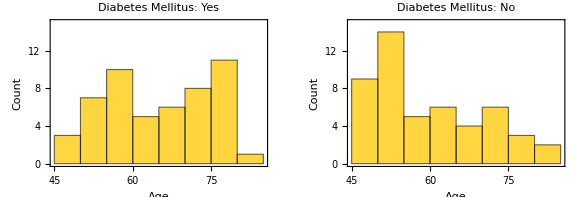

```mathematica
ageCountMax=Max[BinCounts[ageColDMYes,ageBins],BinCounts[ageColDMNo,ageBins]]+1;
GraphicsRow[{
  Histogram[ageColDMYes,ageBins,PlotRange->{ageBins[[{1,2}]],{0,ageCountMax}},
    Frame->True,FrameLabel->{"Age","Count"},PlotLabel->dmYesLabel],
  Histogram[ageColDMNo,ageBins,PlotRange->{ageBins[[{1,2}]],{0,ageCountMax}},
    Frame->True,FrameLabel->{"Age","Count"},PlotLabel->dmNoLabel]
},ImageSize->Large]
```

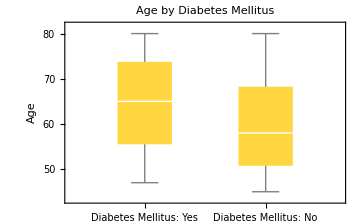

```mathematica
BoxWhiskerChart[{ageColDMYes,ageColDMNo},"Outliers",
  ChartLabels->{dmYesLabel,dmNoLabel},Frame->True,FrameLabel->{None,"Age"},
  PlotLabel->"Age by Diabetes Mellitus",ImageSize->Medium]
```

### CHOL

```mathematica
cholColDMYes=Normal[dmYesData[All,"Chol"]];
cholColDMNo=Normal[dmNoData[All,"Chol"]];
Dataset[<|
  dmYesLabel-><|"Mean"->N[Mean[cholColDMYes]],"Median"->N[Median[cholColDMYes]],
    "StandardDeviation"->N[StandardDeviation[cholColDMYes]],"Quartiles"->N[Quartiles[cholColDMYes]],
    "Min"->Min[cholColDMYes],"Max"->Max[cholColDMYes]|>,
  dmNoLabel-><|"Mean"->N[Mean[cholColDMNo]],"Median"->N[Median[cholColDMNo]],
    "StandardDeviation"->N[StandardDeviation[cholColDMNo]],"Quartiles"->N[Quartiles[cholColDMNo]],
    "Min"->Min[cholColDMNo],"Max"->Max[cholColDMNo]|>
|>]
```

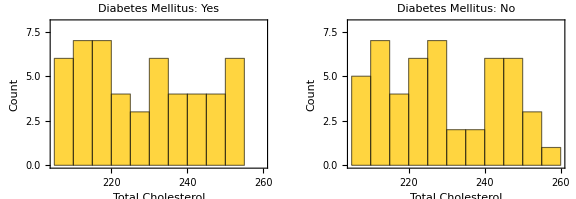

```mathematica
cholCountMax=Max[BinCounts[cholColDMYes,cholBins],BinCounts[cholColDMNo,cholBins]]+1;
GraphicsRow[{
  Histogram[cholColDMYes,cholBins,PlotRange->{cholBins[[{1,2}]],{0,cholCountMax}},
    Frame->True,FrameLabel->{"Total Cholesterol","Count"},PlotLabel->dmYesLabel],
  Histogram[cholColDMNo,cholBins,PlotRange->{cholBins[[{1,2}]],{0,cholCountMax}},
    Frame->True,FrameLabel->{"Total Cholesterol","Count"},PlotLabel->dmNoLabel]
},ImageSize->Large]
```

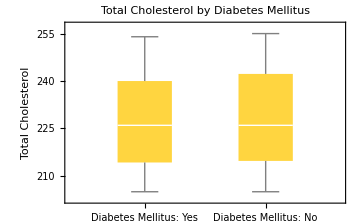

```mathematica
BoxWhiskerChart[{cholColDMYes,cholColDMNo},"Outliers",
  ChartLabels->{dmYesLabel,dmNoLabel},Frame->True,FrameLabel->{None,"Total Cholesterol"},
  PlotLabel->"Total Cholesterol by Diabetes Mellitus",ImageSize->Medium]
```

### DBP

```mathematica
dbpColDMYes=Normal[dmYesData[All,"DBP"]];
dbpColDMNo=Normal[dmNoData[All,"DBP"]];
Dataset[<|
  dmYesLabel-><|"Mean"->N[Mean[dbpColDMYes]],"Median"->N[Median[dbpColDMYes]],
    "StandardDeviation"->N[StandardDeviation[dbpColDMYes]],"Quartiles"->N[Quartiles[dbpColDMYes]],
    "Min"->Min[dbpColDMYes],"Max"->Max[dbpColDMYes]|>,
  dmNoLabel-><|"Mean"->N[Mean[dbpColDMNo]],"Median"->N[Median[dbpColDMNo]],
    "StandardDeviation"->N[StandardDeviation[dbpColDMNo]],"Quartiles"->N[Quartiles[dbpColDMNo]],
    "Min"->Min[dbpColDMNo],"Max"->Max[dbpColDMNo]|>
|>]
```

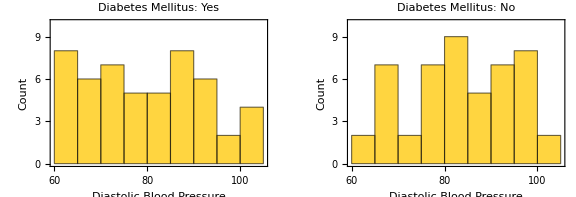

```mathematica
dbpCountMax=Max[BinCounts[dbpColDMYes,dbpBins],BinCounts[dbpColDMNo,dbpBins]]+1;
GraphicsRow[{
  Histogram[dbpColDMYes,dbpBins,PlotRange->{dbpBins[[{1,2}]],{0,dbpCountMax}},
    Frame->True,FrameLabel->{"Diastolic Blood Pressure","Count"},PlotLabel->dmYesLabel],
  Histogram[dbpColDMNo,dbpBins,PlotRange->{dbpBins[[{1,2}]],{0,dbpCountMax}},
    Frame->True,FrameLabel->{"Diastolic Blood Pressure","Count"},PlotLabel->dmNoLabel]
},ImageSize->Large]
```

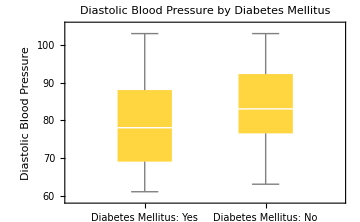

```mathematica
BoxWhiskerChart[{dbpColDMYes,dbpColDMNo},"Outliers",
  ChartLabels->{dmYesLabel,dmNoLabel},Frame->True,FrameLabel->{None,"Diastolic Blood Pressure"},
  PlotLabel->"Diastolic Blood Pressure by Diabetes Mellitus",ImageSize->Medium]
```

### TEMP

```mathematica
tempColDMYes=Normal[dmYesData[All,"Temp"]];
tempColDMNo=Normal[dmNoData[All,"Temp"]];
Dataset[<|
  dmYesLabel-><|"Mean"->Mean[tempColDMYes],"Median"->Median[tempColDMYes],
    "StandardDeviation"->StandardDeviation[tempColDMYes],"Quartiles"->Quartiles[tempColDMYes],
    "Min"->Min[tempColDMYes],"Max"->Max[tempColDMYes]|>,
  dmNoLabel-><|"Mean"->Mean[tempColDMNo],"Median"->Median[tempColDMNo],
    "StandardDeviation"->StandardDeviation[tempColDMNo],"Quartiles"->Quartiles[tempColDMNo],
    "Min"->Min[tempColDMNo],"Max"->Max[tempColDMNo]|>
|>]
```

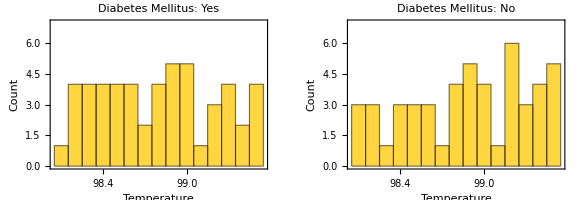

```mathematica
tempCountMax=Max[BinCounts[tempColDMYes,tempBins],BinCounts[tempColDMNo,tempBins]]+1;
GraphicsRow[{
  Histogram[tempColDMYes,tempBins,PlotRange->{tempBins[[{1,2}]],{0,tempCountMax}},
    Frame->True,FrameLabel->{"Temperature","Count"},PlotLabel->dmYesLabel],
  Histogram[tempColDMNo,tempBins,PlotRange->{tempBins[[{1,2}]],{0,tempCountMax}},
    Frame->True,FrameLabel->{"Temperature","Count"},PlotLabel->dmNoLabel]
},ImageSize->Large]
```

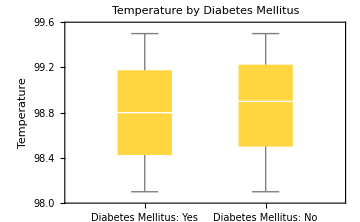

```mathematica
BoxWhiskerChart[{tempColDMYes,tempColDMNo},"Outliers",
  ChartLabels->{dmYesLabel,dmNoLabel},Frame->True,FrameLabel->{None,"Temperature"},
  PlotLabel->"Temperature by Diabetes Mellitus",ImageSize->Medium]
```

### GROUP

```mathematica
groupColDMYes=Normal[dmYesData[All,"Group"]];
groupColDMNo=Normal[dmNoData[All,"Group"]];
groupCountsDMYes=Counts[groupColDMYes];
groupCountsDMNo=Counts[groupColDMNo];
Dataset[AssociationMap[<|
    "Count (" <> dmYesLabel <> ")"->Lookup[groupCountsDMYes,#,0],
    "Proportion (" <> dmYesLabel <> ")"->N[Lookup[groupCountsDMYes,#,0]/Length[groupColDMYes]],
    "Count (" <> dmNoLabel <> ")"->Lookup[groupCountsDMNo,#,0],
    "Proportion (" <> dmNoLabel <> ")"->N[Lookup[groupCountsDMNo,#,0]/Length[groupColDMNo]]
  |> &,groupLevels]]
```

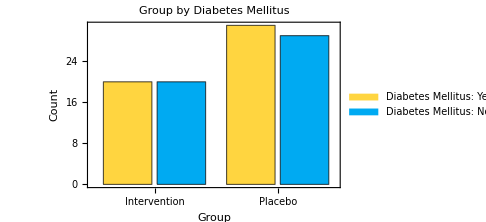

```mathematica
BarChart[
  Table[{Lookup[groupCountsDMYes,level,0],Lookup[groupCountsDMNo,level,0]},{level,groupLevels}],
  ChartLabels->{groupLevels,None},ChartLegends->{dmYesLabel,dmNoLabel},
  Frame->True,FrameLabel->{"Group","Count"},PlotLabel->"Group by Diabetes Mellitus",ImageSize->Medium]
```

### SURVEY

```mathematica
surveyColDMYes=Normal[dmYesData[All,"Survey"]];
surveyColDMNo=Normal[dmNoData[All,"Survey"]];
surveyCountsDMYes=Counts[surveyColDMYes];
surveyCountsDMNo=Counts[surveyColDMNo];
Dataset[AssociationMap[<|
    "Count (" <> dmYesLabel <> ")"->Lookup[surveyCountsDMYes,#,0],
    "Proportion (" <> dmYesLabel <> ")"->N[Lookup[surveyCountsDMYes,#,0]/Length[surveyColDMYes]],
    "Count (" <> dmNoLabel <> ")"->Lookup[surveyCountsDMNo,#,0],
    "Proportion (" <> dmNoLabel <> ")"->N[Lookup[surveyCountsDMNo,#,0]/Length[surveyColDMNo]]
  |> &,surveyLevels] // KeyMap[surveyDecode]]
```

```mathematica
Dataset[<|
  dmYesLabel-><|"Mode"->(surveyDecode /@ Commonest[surveyColDMYes]),
    "Median (score)"->Median[surveyColDMYes],
    "Median (label)"->Lookup[surveyDecode,Median[surveyColDMYes],"Between levels"]|>,
  dmNoLabel-><|"Mode"->(surveyDecode /@ Commonest[surveyColDMNo]),
    "Median (score)"->Median[surveyColDMNo],
    "Median (label)"->Lookup[surveyDecode,Median[surveyColDMNo],"Between levels"]|>
|>]
```

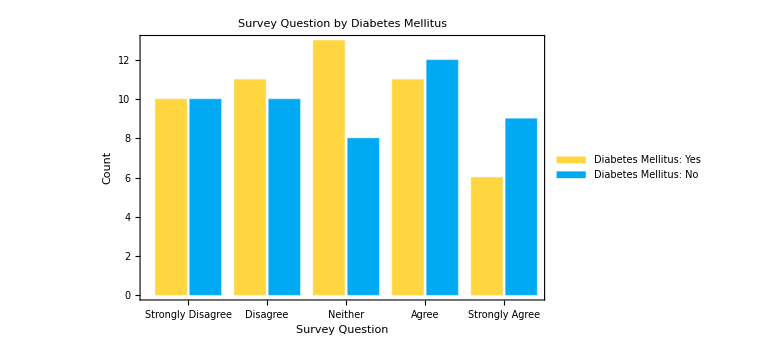

```mathematica
BarChart[
  Table[{Lookup[surveyCountsDMYes,level,0],Lookup[surveyCountsDMNo,level,0]},{level,surveyLevels}],
  ChartLabels->{Lookup[surveyDecode,surveyLevels],None},ChartLegends->{dmYesLabel,dmNoLabel},
  Frame->True,FrameLabel->{"Survey Question","Count"},PlotLabel->"Survey Question by Diabetes Mellitus",
  ImageSize->Large]
```

### ESSENTIALHYPERTENSION

```mathematica
ehColDMYes=Normal[dmYesData[All,"EssentialHypertension"]];
ehColDMNo=Normal[dmNoData[All,"EssentialHypertension"]];
ehCountsDMYes=Counts[ehColDMYes];
ehCountsDMNo=Counts[ehColDMNo];
Dataset[AssociationMap[<|
    "Count (" <> dmYesLabel <> ")"->Lookup[ehCountsDMYes,#,0],
    "Proportion (" <> dmYesLabel <> ")"->N[Lookup[ehCountsDMYes,#,0]/Length[ehColDMYes]],
    "Count (" <> dmNoLabel <> ")"->Lookup[ehCountsDMNo,#,0],
    "Proportion (" <> dmNoLabel <> ")"->N[Lookup[ehCountsDMNo,#,0]/Length[ehColDMNo]]
  |> &,ehLevels] // KeyMap[ehDecode]]
```

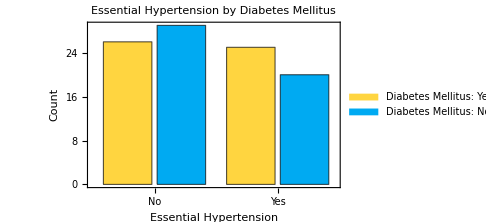

```mathematica
BarChart[
  Table[{Lookup[ehCountsDMYes,level,0],Lookup[ehCountsDMNo,level,0]},{level,ehLevels}],
  ChartLabels->{Lookup[ehDecode,ehLevels],None},ChartLegends->{dmYesLabel,dmNoLabel},
  Frame->True,FrameLabel->{"Essential Hypertension","Count"},
  PlotLabel->"Essential Hypertension by Diabetes Mellitus",ImageSize->Medium]
```